# This script is part of the Supplementary Material for the paper: “MUnCH: a calculator for propagating statistical and other sources of error in passive microrheology” Published in Rheologica Acta, vol. 61, pp. 49--57, 2022

## Authors: Andrés Córdoba and Jay D. Schieber email: andcorduri@gmail.com Copyright (2021) Andrés Córdoba and Jay D. Schieber. This Notebook is distributed under the MIT License.

## Global Parameters and data import

```mathematica
(*This line imports the data file, in this case the first column is time made dimensionless by the smallest relaxation time of the medium and the  second column is voltage in units of mV. For this line to work, save the data file in the same folder as the Notebook*)
SetDirectory[NotebookDirectory[]];
data1=Import["./outputs/Vdata_traj_1.csv"];
(*The next few lines set the values of the global variables that need to be set*)
input=Import["input.csv"];
sens=input[[7,2]] (*sensitivity in nm/mV*);
dsens=0.1* input[[7,2]](*uncertanty in the sensitivity in nm/mV*);
dV=50 (*offset due to electric noise or optical system misalignment in mV*);
DExp=1.53(*probe bead diameter in μm*);
dDExp=0.05*DExp(*uncertanty in the probe bead diameter in μm*);
TExp=20 (*temperature measured during the experiment in ^◦C*);
HeExp=input[[6,2]]  (*trap Stiffness in pN/nm*);
dHeExp=0.10*HeExp (*uncertanty in the trap stiffness in pN/nm*);
Hin=Take[input[[3]],{2,2+input[[2,2]]-1}];
λin=Take[input[[4]],{2,2+input[[2,2]]-1}];
ζ0in=input[[5,2]];
(*"λin" and "Hin" are the relaxation times and moduli of a discrete relaxation spectrum of the fluid used here as input in the BD simulations to generate the data. The "λin" are dimensionless by the smallest relaxation time of the fluid (λ1). The "Hin" are dimensionless by the trap stiffness (He). "ζ0in" is the friction coefficient of the solvent made dimensionless by Heλ1*)
```

## Errors in the mean-squared displacement (MSD) of the probe bead

### Definition of functions for this section

```mathematica
Clear[MSDblT,MSDSamp]
(*This next function, "MSDblT" implements the blocking transformations method (H. Flyvbjerg and H. G. Petersen, The Journal of Chemical Physics, vol. 91, no. 1, pp. 461–466, 1989) for calculating the uncertainty in the MSD. The first argument "data" is the data file where the first column is the time made dimensionless by the smallest relaxation time of the medium, and the second column is voltage in units of mV. The second argument "τj" is the lag time also made dimensionless by the smallest relaxation time of the medium. The third argument "drb" is a vector that contains the measurement errors*)
MSDblT:=Compile[{{data,_Real,2},{τj,_Integer},{drb,_Real,1}},
Module[{xV,xVT,n=Length[data]-τj,j=1,c0,σa,σb,c0p,σap,σbp,xav,dxV,dxAv,dxVT},
xV=Table[(data[[i,2]]-data[[i+τj,2]])^2,{i,1,n}];xav=Mean[xV];
dxV=Table[2*√(xV[[i]](drb[[i]]^2+drb[[i+τj]]^2)),{i,1,n}];
dxAv=(√Sum[dxV[[i]]^2,{i,1,Length[dxV]}])/n;
c0=1/n Sum[(xV[[i]]-xav)^2,{i,1,n}];
σa=√(c0/(n-1))+dxAv;σb=σa/(√(2(n-1)));n=Floor[n/2];
xVT=Table[1/2(xV[[2*i-1]]+xV[[2*i]]),{i,1,n}];
dxVT=Table[1/2(√(dxV[[2*i-1]]^2+dxV[[2*i]]^2)),{i,1,n}];
dxAv=(√Sum[dxVT[[i]]^2,{i,1,Length[dxVT]}])/n;
c0p=1/n Sum[(xVT[[i]]-xav)^2,{i,1,n}];σap=√(c0p/(n-1))+dxAv;σbp=σap/(√(2(n-1)));
While[Abs[σa-σap]>σbp+σb&&n>4,
σa=σap;σb=σbp;xV=xVT;dxV=dxVT;j=j+1;n=Floor[n/2];
xVT=Table[1/2(xV[[2*i-1]]+xV[[2*i]]),{i,1,n}];
dxVT=Table[1/2(√(dxV[[2*i-1]]^2+dxV[[2*i]]^2)),{i,1,n}];
dxAv=(√Sum[dxVT[[i]]^2,{i,1,Length[dxVT]}])/n;
c0p=1/n Sum[(xVT[[i]]-xav)^2,{i,1,n}];
σap=√(c0p/(n-1))+dxAv;σbp=σap/(√(2(n-1)))];{xav,σap}]]
(*This next function, "MSDSamp" calls the previous functions at evenly spaced points in a log scale,i.e. it calculates the MSD and its uncertainty at evenly spaced lag times in a log scale. The first argument "data" is the data file, The second argument "sens" is the sensitivity in units of nm/mV. The fourth argument "dsens" is the uncertainty in the sensitivity in units of nm/mV. The fourth argument "dV" is the offset due to electric noise or optical system misalignment in units of mV*)
MSDSamp[data_,sens_,dsens_,dV_]:=Module[{res1,drb,datax,sampf,p=8,m=2},
sampf=1/(data[[2,1]]-data[[1,1]]);
drb=Table[√((data[[i,2]]*dsens)^2+(sens*dV)^2),{i,1,Length[data]}];
datax={#[[1]],#[[2]]*sens}&/@data;
res1=Table[Prepend[MSDblT[datax,j,drb],N[j/sampf]],{j,1,p*m-1}];Do[res1=Join[res1,Table[Prepend[MSDblT[datax,j,drb],N[j/sampf]],{j,p*m^i,p*m^(i+1)-1,m^i}]],{i,1,Floor[Log[Length[data]/p]/Log[m]]-1}];res1]
```

```mathematica
Clear[PowerTicks,ErrBarP]
(*The function "ErrBarP" is for plotting the error bars in a log-log plot*)
ErrBarP[data_/;MatrixQ[data,NumericQ],err_/;VectorQ[err,NumericQ],del_?NumericQ,color_]:=
Module[{data2,data3,err2},
data2=Select[MapThread[{#1[[1]],#1[[2]],#2}&,{data,err}],#[[2]]-#[[3]]>0&&#[[2]]+#[[3]]>0&];
data3={#[[1]],#[[2]]}&/@data2;err2=#[[3]]&/@data2;
{{color,MapThread[Line[{Log[{#1[[1]],(#1[[2]]-#2)}],Log[{#1[[1]],(#1[[2]]+#2)}]}]&,{data3,err2}]},{color,MapThread[Line[{{Log[#1[[1]]]-del,Log[(#1[[2]]-#2)]},{Log[#1[[1]]]+del,Log[(#1[[2]]-#2)]}}]&,{data3,err2}]},{color,MapThread[Line[{{Log[#1[[1]]]-del,Log[(#1[[2]]+ #2)]},{Log[#1[[1]]]+del,Log[(#1[[2]]+#2)]}}]&,{data3,err2}]}}]
(*The function "PowerTicks" is for displaying frame ticks in as powers of ten in a log-log plot (Mathematica does not do this by default)*)
PowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i],Spacer[{0,0}]]},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0.},{Thickness[0.001]}},{i,min10,max10},{k,9}],1]]]
```

### Plotting the MSD with error bars

```mathematica
(*This line calls the function that calculates the MSD and its uncertainty. This might take a while,depending on the size of the file and your computer*)
MSDS={MSDSamp[data1,sens,dsens,dV]};
```

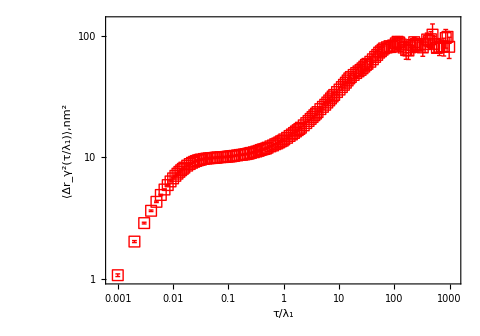

```mathematica
(*This next few lines plot the MSD with error bars calculated using the blocking transformations*)
color={Red,Blue,Magenta,Orange,Black,Pink};
errbarsMSD=Table[ErrBarP[{#[[1]],#[[2]]}&/@MSDS[[i]],#[[3]]&/@MSDS[[i]],0.1,color[[i]]],{i,1,Length[MSDS]}];
MSDP=Table[{#[[1]],#[[2]]}&/@MSDS[[i]],{i,1,Length[MSDS]}];
P1=ListLogLogPlot[MSDP,PlotRange->{{8*10^-4,1.2*10^3},{1*10^0,1.3*10^2}},PlotMarkers->{Style["□",Red,11],Style["◦",Blue,11],Style["△",Darker[Green],12],Style["◦",Blue,11],Style["▯",Magenta,12],Style["□",Orange,11],Style["♢",Black,11],Style["▽",Pink,11],Style["♢",Brown,11]},Axes->False,Frame->True,Joined->False,AspectRatio->0.7,ImageSize->480,BaseStyle->{FontSize->18,FontFamily->"Arial"},FrameLabel->{"τ/λ_1","⟨Δr_γ^2(τ/λ_1)⟩,nm^2"},FrameTicks->{{PowerTicks[True],PowerTicks[False]},{PowerTicks[True],PowerTicks[False]}},Epilog->{errbarsMSD}]
```

```mathematica
(*This line exports the MSD and its uncertanty. The first column in the written file is time made dimensionless by the smallest relaxation time of the medium. The second column is the MSD in nm^2. The third column is the MSD error also in nm^2*)
Export["./outputs/MSD_wth_err_math.csv",MSDS[[1]]];
```

## Fitting the MSD

### Definition of functions for this section

```mathematica
Clear[InMSD]
(*Given the relaxation times "λ" and moduli "H" of a discrete relaxation spectrum of the fluid,the function "InMSD" calculates the parameters for an analytic expression of the MSD, see A. Córdoba, T. Indei, and J. D. Schieber, Journal of Rheology, vol. 56, no. 1, pp. 185–212,2012 for details. The expression is useful to obtain an initial guess for the fitting routine. The notation used here is the same as the one used in the referenced paper*)
InMSD[H_,λ_,ζ0_,cp_,s_]:=Module[{poly1,poly2,poly3,n,Λp,ΛpV,Λpsol,Λpsolrep,sol1,sol2,sol3,cpsol,ecs,roots},
n=Length[H];poly1=Expand[∑_(j=1)^(n+1) (cp[j]*∏_(i=1)^(n+1) If[i≠j,(s+1/Λp[i]),1])];
poly2=Expand[∏_(j=1)^n (s+1/λ[[j]])+ s(ζ0∏_(j=1)^n (s+1/λ[[j]])+∑_(j=1)^n (H[[j]]*∏_(i=1)^n If[i≠j,(s+1/λ[[i]]),1]))];
poly3=Expand[ (ζ0∏_(j=1)^n (s+1/λ[[j]])+∑_(j=1)^n (H[[j]]*∏_(i=1)^n If[i≠j,(s+1/λ[[i]]),1]))];
roots=Solve[poly2==0,s];Λpsol=-1/(s/.roots);Λpsolrep=Table[Λp[i]->Λpsol[[i]],{i,1,Length[Λpsol]}];
sol1=CoefficientList[poly1/.Λpsolrep,s];sol2=CoefficientList[poly3,s];
ecs=Table[sol1[[i]]==sol2[[i]],{i,1,Length[Λpsol]}];sol3=Solve[ecs,Table[cp[i],{i,1,Length[Λpsol]}]];
cpsol=Table[cp[i]/.sol3[[1]],{i,1,Length[Λpsol]}];{cpsol,Λpsol}]
```

```mathematica
Clear[MSDf,fitMSD]
(*The function "MSDf" is the analytic expression used to fit the MSD of the probe bead. The first argument "Tin" is the temperature measured during the experiment in ^◦C. The second argument "Hein" is the trap stiffness in pN/nm*)
MSDf[Tin_,Hein_,cp_,Λp_,t_]:=Module[{kB=1.38*10^-23,T=Tin+273.15,He=Hein*10^-12/10^-9},(10^9)^2(2kB T)/He(1-Sum[cp[[i]]*Exp[-t/Λp[[i]]],{i,1,Length[cp]}]/Sum[cp[[i]],{i,1,Length[cp]}])]
(*The function "fitMSD" fits the function above to the data, using the MSD errors as the weights in the χ^2 function*)
fitMSD[Tin_,Hein_,H_,λ_,ζ0_,data_,uncert_]:=Module[{sol,λv,t,pars,err,cpv,s,InGuess,nm},
InGuess=InMSD[H,λ,ζ0,cpv,s];
nm=Length[InGuess[[1]]];
sol=NonlinearModelFit[data,{MSDf[Tin,Hein,Table[cp[i],{i,1,nm}],InGuess[[2]],t],Table[cp[i]≥0,{i,1,nm}]},Table[{cp[i],InGuess[[1,i]]/Total[InGuess[[1]]]},{i,1,nm}],{t},VarianceEstimatorFunction->(1&),Weights->(1/#^2&/@uncert)];
pars=sol["BestFitParameters"];
{Join[pars,Table[Λp[i]->InGuess[[2,i]],{i,1,nm}]],Quiet[sol["CovarianceMatrix"]]}]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

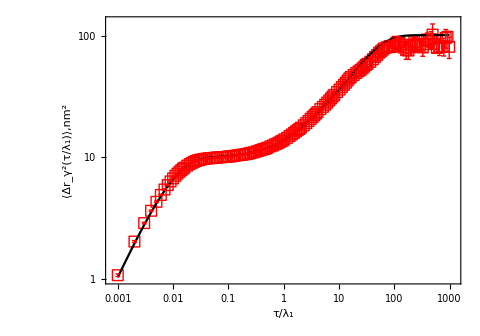

```mathematica
fitsol=fitMSD[TExp,HeExp,Hin,λin,ζ0in,MSDP[[1]],#[[3]]&/@MSDS[[1]]];
PF1=LogLogPlot[MSDf[TExp,HeExp,Table[cp[i],{i,1,Length[Hin]+1}],Table[Λp[i],{i,1,Length[Hin]+1}],t]/.fitsol[[1]],{t,10^-3,10^3},PlotRange->{{8*10^-4,1.1*10^3},{1*10^0,1.3*10^2}},PlotStyle->{{Black}},Axes->False,Frame->True,AspectRatio->0.7,ImageSize->480,BaseStyle->{FontSize->18,FontFamily->"Arial"},FrameLabel->{"τ/λ_1","⟨Δr_γ^2(τ/λ_1)⟩,nm^2"}];
Needs["PlotLegends`"]
Legend0={{{Style["□",Red,15],Text[Style["MSD viscoelastic",FontSize->16,FontFamily->"Arial",Red]]},{Graphics[{Black,Thick,Line[{{0,0},{2,0}}]}],Text[Style["Fit",FontSize->16,FontFamily->"Arial"]]}},LegendShadow->False,LegendSize->{0.7,0.23},LegendPosition->{0.1,-0.35},LegendTextSpace->6,LegendBorder->False};
P1F=ShowLegend[Show[P1,PF1],Legend0]
```

```mathematica
(*The next line exports the plot shown above in eps and jpeg formats*)
Export["./outputs/plot_msd_math.eps",P1F];Export["./outputs/plot_msd_math.jpeg",P1F];
```

```mathematica
(*The next line exports the parameters of the fitted MSD function to a file*)
Export["./outputs/msd_fit_math.csv",Table[{Λp[i],cp[i]/Sum[cp[j],{j,1,Length[Hin]+1}]},{i,1,Length[Hin]+1}]/.fitsol[[1]]];
```

## Propagation of error to the dynamic modulus

### Definition of functions for this section

```mathematica
Clear[Gs]
(*The function "Gs" propagates the error from the MSD fit to the dynamic modulus. It uses the generalized Stokes-Einstein relation (GSER). It also includes the uncertainties in the bead radius and the trap stiffness in the calculation, see main text for details*)
Gs[Tin_,Hein_,dHein_,Din_,dDin_,cp_,Λp_,n_,fit_,s_]:=Module[{MSDb,kB=1.38*10^-23,T=Tin+273.15,He=Hein*10^-12/10^-9,R=Din/2*10^-6,Gsin,GsErr,dR,dHe,Rvar,Hevar,GsErrOp,GsErrOp2},
dR=dDin/2*10^-6;dHe=dHein*10^-12/10^-9;
MSDb=(2kB T)/Hevar(1/s-(∑_(j=1)^n (cp[j]*∏_(i=1)^n If[i≠j,(s+1/Λp[i]),1]))/((∑_(j=1)^n cp[j])∏_(i=1)^n (s+1/Λp[i])));
Gsin=(kB T)/(3π Rvar s MSDb)-Hevar/(6π Rvar);
GsErr=Sqrt[(D[Gsin,Rvar]*dR)^2+(D[Gsin,Hevar]*dHe)^2+Sum[D[Gsin,cp[i]]*D[Gsin,cp[j]]*fit[[2,i,j]],{i,1,n},{j,1,n}]];
{FullSimplify[Gsin/.{Hevar->He,Rvar->R}/.fit[[1]]],FullSimplify[GsErr/.{Hevar->He,Rvar->R}/.fit[[1]]]}]
```

```mathematica
(*The function "GsKn" is for ploting the known analytic dynamic modulus that is used as input in the BD simulations used here to generate the data*)
Clear[GsKn]
GsKn[Hein_,Din_,h_,λ_,μ0_,ω_]:=Module[{He=Hein*10^-12/10^-9,R=Din/2*10^-6}, He/(6 π R)(μ0 I ω+Sum[(h[[i]]λ[[i]]I ω)/(1+λ[[i]]I ω),{i,1,Length[h]}])]
```

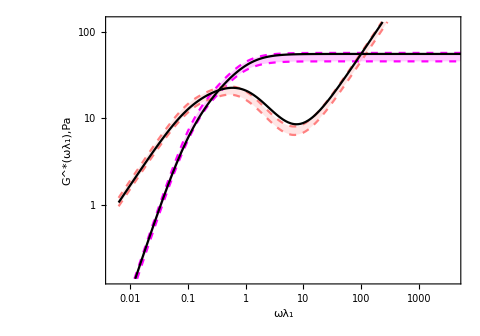

```mathematica
Geval=Gs[TExp,HeExp,dHeExp,DExp,dDExp,cp,Λp,Length[Hin]+1,fitsol,s];
Gp={2π/#[[1]],Re[Geval[[1]]/.s-> 2π I/#[[1]]]}&/@MSDP[[1]];
GpUp={2π/#[[1]],Re[Geval[[1]]+Geval[[2]]/.s-> 2π I/#[[1]]]}&/@MSDP[[1]];
GpDo={2π/#[[1]],Re[Geval[[1]]-Geval[[2]]/.s-> 2π I/#[[1]]]}&/@MSDP[[1]];
Gpp={2π/#[[1]],Im[Geval[[1]]/.s-> 2π I/#[[1]]]}&/@MSDP[[1]];
GppUp={2π/#[[1]],Im[Geval[[1]]+Geval[[2]]/.s-> 2π I/#[[1]]]}&/@MSDP[[1]];
GppDo={2π/#[[1]],Im[Geval[[1]]-Geval[[2]]/.s-> 2π I/#[[1]]]}&/@MSDP[[1]];
GpIn={2π/#[[1]],Re[GsKn[HeExp,DExp,Hin,λin,ζ0in,ω]/.ω-> 2π/#[[1]]]}&/@MSDP[[1]];
GppIn={2π/#[[1]],Im[GsKn[HeExp,DExp,Hin,λin,ζ0in,ω]/.ω-> 2π/#[[1]]]}&/@MSDP[[1]];
Needs["PlotLegends`"]
Legend0={{{Graphics[{Magenta,Dashed, Thick,Line[{{0,0},{4,0}}]}],Text[Style["G'(ω)",FontSize->16,FontFamily->"Arial",Magenta]]},{Graphics[{Pink, Dashed,Thick,Line[{{0,0},{4,0}}]}],Text[Style["G''(ω)",FontSize->16,FontFamily->"Arial",Pink]]}},LegendShadow->False,LegendSize->{0.4,0.21},LegendPosition->{0.3,-0.35},LegendTextSpace->2,LegendBorder->False};
P2=ShowLegend[ListLogLogPlot[{Sort[GpDo],Sort[GppDo],Sort[GpUp],Sort[GppUp],Sort[GpIn],Sort[GppIn]},PlotRange->{{5*10^-3,4*10^3},{1.4*10^-1,1.3*10^2}},Joined->{True,True,True,True,True,True}, PlotStyle->{{Magenta,Dashed},{Pink,Dashed},{Magenta,Dashed},{Pink,Dashed},{Black},{Black}},Axes->False,Frame->True,Joined->False,AspectRatio->0.7,ImageSize->480,BaseStyle->{FontSize->18,FontFamily->"Arial"},FrameLabel->{"ωλ_1","G^*(ωλ_1),Pa"},FrameTicks->{{PowerTicks[True],PowerTicks[False]},{PowerTicks[True],PowerTicks[False]}},Filling->{1->{3},2->{4}}],Legend0]
```

```mathematica
(*The next line exports the plot shown above in eps and jpeg formats*)
Export["./outputs/plot_G_math.eps",P2];Export["./outputs/plot_G_math.jpeg",P2];
```

```mathematica
(*The next line exports the G^*(ω) and its uncertanty to a file. The first column in the frequency, the second column is the storage modulus, the third column is the uncertainty in the storage modulus, the fourth column in the loss modulus, and the fifth column is the uncertainty in the loss modulus. The units are the same as in the plot shown above*)
Export["./outputs/Gs_wth_err_math.csv",Sort[MapThread[{#1[[1]],#1[[2]],#2[[2]]-#1[[2]],#3[[2]],#4[[2]]-#3[[2]]}&,{Gp,GpUp,Gpp,GppUp}]]];
```